## Modeling the molecular impact of the SARS-CoV-2 infection on the renin-angiotensin system

F.Pucci, P. Bogaerts, M. Rooman
Computational Biology and Bioinformatics, 3BIO department
Biosystems Modeling and Control, 3BIO department
Université Libre de Bruxelles, Bruxelles, Belgium
Contact us at : fapucci@ulb.ac.be, philippe.bogaerts@ulb.ac.be, mrooman@ulb.ac.be

## Section 1. Model Parameters

```mathematica
ClearAll["Global`*"]
```

```mathematica
ln2=N[Log[2]];
Color[0]=Blue;Color[1]=Red;
```

In the following, the blue and red curves will correspond to normotensive and hypertensive individuals, respectively.

A) Dynamical equations of the RAS model for normotensive  (i=0) and hypertensive (i=1) individuals schematically depicted here.

#### Concentrations (fmol/ml)

(RE = Renin,  AGT = angiotensinogen, AI = Angiotensin I,  AII = Angiotensin II, A17 = Angiotensin 1-7, AIV = Angiotensin IV, MASb = A17-MAS  complex,  AT1Rb = AII-Angiotensin II Receptor Type I  complex, AT2Rb = AII-Angiotensin II Receptor Type II  complex )

#### Rates (fmol/(ml min)) and parameters

(kagt = AGT  production rate, cre = renin reaction rate, hagt= AGT half life, hre= renin half life, β0 = feedback loop parameter, β1 = feedback loop parameter, cace = reaction rate AI --> AII via ACE, haI = AI half life, cace2 = reaction rate AII --> A17 via ACE2, caIV = reaction rate AII --> AIV, cat1R = reaction rate AT1R-AII complex formation, cat2R = reaction rate AT2R-AngII complex formation, haII = AII half life, cmas = reaction rate A17-MAS complex formation, ha17 = A17 half life, haIV = AIV half life, hat1r = AT1Rb complex half life,  hat2r =AT2Rb half life, hmas = MASb half life)

#### Clinical data

(O2 = PaO2/FiO2 (mmHg), Tension = diastolic blood pressure )

```mathematica
EQS:={For[i=0,i<2,i++,eqAGT[i]=kagt[i]-cre[i] RE[i][t]-ln2/hagt AGT[i][t]],
For[i=0,i<2,i++,eqRE[i]=β0 [i]+β1[i]((AT1Rb[i][t]/AT1Rb0[0])^(-A)-1)-ln2/hre  RE[i][t]],
For[i=0,i<2,i++,eqAI[i]=cre[i] RE[i][t]-cace[i]AI[i][t]-ln2/haI AI[i][t]],
For[i=0,i<2,i++,eqAII[i]=cace[i]AI[i][t]-(cace2[i]+caIV[i]+cat1R[i]+cat2R[i])AII[i][t]-ln2/haII AII[i][t]],
For[i=0,i<2,i++,eqA17[i]=cace2[i] AII[i][t]-cmas[i] A17[i][t] -ln2/ha17 A17[i][t]],
For[i=0,i<2,i++,eqAIV[i]=caIV[i]  AII[i][t]-ln2/haIV  AIV[i][t]],
For[i=0,i<2,i++,eqAT1Rb[i]=cat1R[i] AII[i][t]-ln2/hat1R AT1Rb[i][t]],
For[i=0,i<2,i++,eqAT2Rb[i]=cat2R[i] AII[i][t]-ln2/hat2R  AT2Rb[i][t]],
For[i=0,i<2,i++,eqMASb[i]=cmas[i] A17[i][t]-ln2/hmas  MASb[i][t]],
For[i=0,i<2,i++,O2[i][t]=267.0(- AII[i][t]/AII0[i]+ A17[i][t]/A170[i])+450.0],
For[i=0,i<2,i++,Tension[i][t]=(AT1Rb[i][t]/AT1Rb0[0])*6.4+73.6]};
```

B) The values of peptide concentrations and  half lives for healthy normotensive and hypertensive individuals collected from the literature (Tables 1 and 2 of the main text).

```mathematica
AGT[0][0]=600000.;AGT[1][0]=600000.;
AI[0][0]=70.;AI[1][0]=110.;
AII[0][0]=28.;AII[1][0]=156.;
A17[0][0]=36.;A17[1][0]=92.;
AIV[0][0]=1.;AIV[1][0]=1.;
AT1Rb[0][0]=15.0;AT1Rb[1][0]=85.0;
AT2Rb[0][0]=5.0;AT2Rb[1][0]=27.0;
For[i=0,i<2,i++,AT1Rb0[i]=AT1Rb[i][0]];

hagt=600;
haI=0.5;
haII=0.5;
ha17=0.5;
haIV=0.5;
hat1R=12;
hat2R=12;
hmas=12;
hre=12;

For[i=0,i<2,i++,cre[i]=20];
For[i=0,i<2,i++,cmas[i]=cat2R[i]];
For[i=0,i<2,i++,β1[i]=1];
A=0.8;
```

C) Solution of the model at  equilibrium to obtain the values of the unknown parameters and concentrations (kagt, cace, cace2, caIV, cat1R, cat2R, β0, MASb and RE)

```mathematica
t=0;EQS;For[i=0,i<2,i++,sol[i]=Solve[{0==eqAGT[i],0==eqRE[i],0==eqAI[i],0==eqAII[i],0==eqA17[i],0==eqAIV[i],0==eqAT1Rb[i],0==eqAT2Rb[i],0==eqMASb[i]},
{ kagt[i],cace[i],cace2[i],caIV[i],cat1R[i],cat2R[i],β0[i],MASb[i][t],RE[i][t]}]]
```

```mathematica
For[i=0,i<2,i++,kagt[i]=kagt[i]/.sol[i][[1]]]
For[i=0,i<2,i++,cace[i]=cace[i]/.sol[i][[1]]]
For[i=0,i<2,i++,cace2[i]=cace2[i]/.sol[i][[1]]]
For[i=0,i<2,i++,caIV[i]=caIV[i]/.sol[i][[1]]]
For[i=0,i<2,i++,cat1R[i]=cat1R[i]/.sol[i][[1]]]
For[i=0,i<2,i++,cat2R[i]=cat2R[i]/.sol[i][[1]]]
For[i=0,i<2,i++,β0[i]=β0[i]/.sol[i][[1]]]
For[i=0,i<2,i++,MASb[i][0]=MASb[i][0]/.sol[i][[1]]]
For[i=0,i<2,i++,RE[i][0]=RE[i][0]/.sol[i][[1]]]
```

```mathematica
For[i=0,i<2,i++,AGT0[i]=AGT[i][0]];
For[i=0,i<2,i++,RE0[i]=RE[i][0]];
For[i=0,i<2,i++,AI0[i]=AI[i][0]];
For[i=0,i<2,i++,AII0[i]=AII[i][0]];
For[i=0,i<2,i++,A170[i]=A17[i][0]];
For[i=0,i<2,i++,AIV0[i]=AIV[i][0]];
For[i=0,i<2,i++,AT1Rb0[i]=AT1Rb[i][0]];
For[i=0,i<2,i++,AT2Rb0[i]=AT2Rb[i][0]];
For[i=0,i<2,i++,MASb0[i]=MASb[i][0]];
For[i=0,i<2,i++,cchym[i]=cchym[i]];
For[i=0,i<2,i++,cnep[i]=cnep[i]];
```

```mathematica
Clear[AGT,RE,AI,AII,A17,AIV,AT1Rb,AT2Rb,MASb,t];
```

## Section 2. Dynamical Modeling

```mathematica
EQS;For[i=0,i<2,i++,sol[i]=NDSolve[{D[AGT[i][t],t]==eqAGT[i],D[RE[i][t],t]==eqRE[i],D[AI[i][t],t]==eqAI[i],D[AII[i][t],t]==eqAII[i],
D[A17[i][t],t]==eqA17[i],D[AIV[i][t],t]==eqAIV[i],D[AT1Rb[i][t],t]==eqAT1Rb[i],D[AT2Rb[i][t],t]==eqAT2Rb[i],D[MASb[i][t],t]==eqMASb[i],
AGT[i][0]==600000,RE[i][0]==10,AI[i][0]==10,AII[i][0]==10,A17[i][0]==10,AIV[i][0]==10,AT1Rb[i][0]==10,AT2Rb[i][0]==10,MASb[i][0]==0},{ AGT[i],RE[i],AI[i],AII[i],A17[i],AIV[i],AT1Rb[i],AT2Rb[i],MASb[i]},{t,0,100000000}]]
```

#### Example of Plot: dynamical evolution of A17

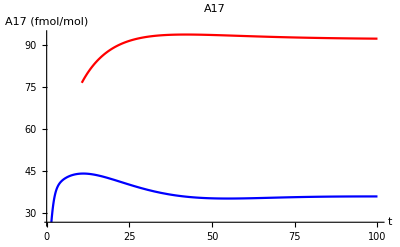

```mathematica
For[i=0,i<2,i++,p[i]=Plot[Evaluate[(A17[i][t])/.sol[i]],{t,0,100},PlotStyle->Color[i]]];Show[p[0],p[1],PlotRange->All,PlotLabel->"A17",AxesLabel->{"t","A17 (fmol/mol)"}]
```

## Section 3. Impact of RAS-blockers on RAS and Diastolic Blood Pressure

```mathematica
Clear[sol,p]
```

### Modeling Drug effects: Introducing γ functions

```mathematica
For[i=0,i<2,i++,cacef[i]=cace[i]];
For[i=0,i<2,i++,cace[i]=cacef[i](1-γacei)];
For[i=0,i<2,i++,cat1Rf[i]=cat1R[i]];
For[i=0,i<2,i++,cat1R[i]=cat1Rf[i](1-γarb)];
For[i=0,i<2,i++,cref[i]=cre[i]];
For[i=0,i<2,i++,cre[i]=cref[i](1-γdri)];
```

### Direct Renin Inhibitor (DRI) Drugs

Analysis of the impact of DRI on RAS. Its effect is mimicked by the factor γdri. Different values of γdri are considered: γdri = 0.1*i (i=0,5) .

```mathematica
For[j=0,j<6,j++,
γdri=j*0.1;γacei=0;γarb=0;EQS;For[i=0,i<2,i++,sol[i][j]=NDSolve[{D[AGT[i][t],t]==eqAGT[i],D[RE[i][t],t]==eqRE[i],D[AI[i][t],t]==eqAI[i],D[AII[i][t],t]==eqAII[i],
D[A17[i][t],t]==eqA17[i],D[AIV[i][t],t]==eqAIV[i],D[AT1Rb[i][t],t]==eqAT1Rb[i],D[AT2Rb[i][t],t]==eqAT2Rb[i],D[MASb[i][t],t]==eqMASb[i],
AGT[i][0]==AGT0[i],RE[i][0]==RE0[i],AI[i][0]==AI0[i],AII[i][0]==AII0[i],A17[i][0]==A170[i],AIV[i][0]==AIV0[i],AT1Rb[i][0]==AT1Rb0[i],AT2Rb[i][0]==AT2Rb0[i],MASb[i][0]==MASb0[i]},{ AGT[i],RE[i],AI[i],AII[i],A17[i],AIV[i],AT1Rb[i],AT2Rb[i],MASb[i]},{t,0,200000}]]];
```

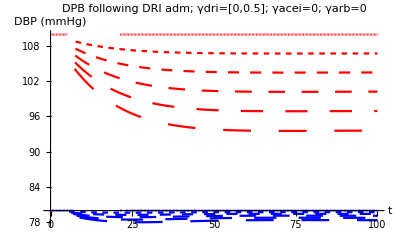

```mathematica
For[j=0,j<6,j++,For[i=0,i<2,i++,p[i][j]=Plot[Evaluate[Tension[i][t]/.sol[i][j]],{t,0,100},PlotStyle->{Color[i],Dashing[j/100]}]]];Show[p[0][0],p[0][1],p[0][2],p[0][3],p[0][4],p[0][5],p[1][0],p[1][1],p[1][2],p[1][3],p[1][4],p[1][5],PlotRange->All,PlotLabel->"DPB following DRI adm; γdri=[0,0.5]; γacei=0; γarb=0",AxesLabel->{"t","DBP (mmHg)"}]
```

### ACE Inhibitor (ACE-I) Drugs

Analysis of the impact of ACE-I on RAS. Its effect is mimicked by the factor γacei. Different values of γacei are considered: γacei = 0.1*i (i=0,5) are considered.

```mathematica
For[j=0,j<6,j++,γacei=j*0.1;γdri=0;γarb=0;EQS;For[i=0,i<2,i++,sol[i][j]=NDSolve[{D[AGT[i][t],t]==eqAGT[i],D[RE[i][t],t]==eqRE[i],D[AI[i][t],t]==eqAI[i],D[AII[i][t],t]==eqAII[i],
D[A17[i][t],t]==eqA17[i],D[AIV[i][t],t]==eqAIV[i],D[AT1Rb[i][t],t]==eqAT1Rb[i],D[AT2Rb[i][t],t]==eqAT2Rb[i],D[MASb[i][t],t]==eqMASb[i],
AGT[i][0]==AGT0[i],RE[i][0]==RE0[i],AI[i][0]==AI0[i],AII[i][0]==AII0[i],A17[i][0]==A170[i],AIV[i][0]==AIV0[i],AT1Rb[i][0]==AT1Rb0[i],AT2Rb[i][0]==AT2Rb0[i],MASb[i][0]==MASb0[i]},{ AGT[i],RE[i],AI[i],AII[i],A17[i],AIV[i],AT1Rb[i],AT2Rb[i],MASb[i]},{t,0,200000}]]];
```

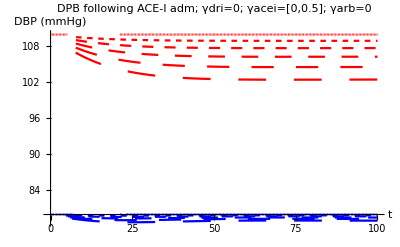

```mathematica
For[j=0,j<6,j++,For[i=0,i<2,i++,p[i][j]=Plot[Evaluate[Tension[i][t]/.sol[i][j]],{t,0,100},PlotStyle->{Color[i],Dashing[j/100]}]]];Show[p[0][0],p[0][1],p[0][2],p[0][3],p[0][4],p[0][5],
p[1][0],p[1][1],p[1][2],p[1][3],p[1][4],p[1][5],PlotRange->All,PlotLabel->"DPB following ACE-I adm; γdri=0; γacei=[0,0.5]; γarb=0",AxesLabel->{"t","DBP (mmHg)"}]
```

Comparison with experimental data from large cohorts of patients (see Result section of the paper)

```mathematica
tf=10000;
For[k=0,k<41,k++,γacei=k*0.0125;γdri=0;γarb=0;
EQS;
For[i=0,i<2,i++,sol[i][k]=Solve[{0==eqAGT[i],0==eqRE[i],0==eqAI[i],0==eqAII[i],
0==eqA17[i],0==eqAIV[i],0==eqAT1Rb[i],0==eqAT2Rb[i],0==eqMASb[i]},{ AGT[i][t],RE[i][t],AI[i][t],AII[i][t],A17[i][t],AIV[i][t],AT1Rb[i][t],AT2Rb[i][t],MASb[i][t]}]]];
```

```mathematica
Needs["ErrorBarPlots`"]
```

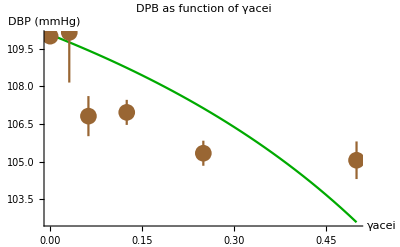

```mathematica
Show[ListPlot[Table[{0.0125*k,(73.6+0.429 AT1Rb [i][t]/.sol[i][k][[1]])},{i,1,1},{k,0,40}],Joined->True,PlotStyle->{Darker[Green]}],
ErrorListPlot[{{{0,110},ErrorBar[0]},{{0.5/16,110.15},ErrorBar[2.0]},{{0.5/8,110-3.19},ErrorBar[0.8]},{{0.5/4,110-3.04},ErrorBar[0.5]},{{0.5/2,110-4.67},ErrorBar[0.5]},{{0.5,110-4.95},ErrorBar[0.75]}},PlotStyle->{Brown,PointSize[0.03]}],PlotLabel->"DPB as function of γacei",AxesLabel->{"γacei","DBP (mmHg)"}]
```

### AT1R Receptor Blocker (ARB) Drugs

Analysis of the impact of ARB on RAS. Its effect is mimicked by the factor γarb.  Different values of are γarb considered: γarb = 0.1*i (i=0,5) are considered.

```mathematica
For[j=0,j<6,j++,γarb=j*0.1;γacei=0;γdri=0;EQS;For[i=0,i<2,i++,sol[i][j]=NDSolve[{D[AGT[i][t],t]==eqAGT[i],D[RE[i][t],t]==eqRE[i],D[AI[i][t],t]==eqAI[i],D[AII[i][t],t]==eqAII[i],
D[A17[i][t],t]==eqA17[i],D[AIV[i][t],t]==eqAIV[i],D[AT1Rb[i][t],t]==eqAT1Rb[i],D[AT2Rb[i][t],t]==eqAT2Rb[i],D[MASb[i][t],t]==eqMASb[i],
AGT[i][0]==AGT0[i],RE[i][0]==RE0[i],AI[i][0]==AI0[i],AII[i][0]==AII0[i],A17[i][0]==A170[i],AIV[i][0]==AIV0[i],AT1Rb[i][0]==AT1Rb0[i],AT2Rb[i][0]==AT2Rb0[i],MASb[i][0]==MASb0[i]},{ AGT[i],RE[i],AI[i],AII[i],A17[i],AIV[i],AT1Rb[i],AT2Rb[i],MASb[i]},{t,0,200000}]]];
```

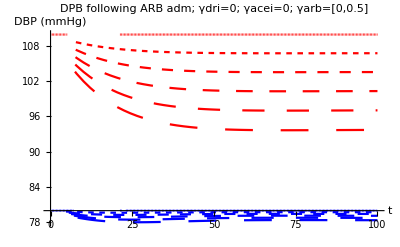

```mathematica
For[j=0,j<6,j++,For[i=0,i<2,i++,p[i][j]=Plot[Evaluate[Tension[i][t]/.sol[i][j]],{t,0,100},PlotStyle->{Color[i],Dashing[j/100]}]]];Show[p[0][0],p[0][1],p[0][2],p[0][3],p[0][4],p[0][5],
p[1][0],p[1][1],p[1][2],p[1][3],p[1][4],p[1][5],PlotRange->All,PlotLabel->"DPB following ARB adm; γdri=0; γacei=0; γarb=[0,0.5]",AxesLabel->{"t","DBP (mmHg)"}]
```

### RAS-blockers combination

Analysis of the impact of the combination of  ACE-I, ARB and DRI. Different values of γace, γdri and γarb [0-0.5] are considered.

```mathematica
For[j=0,j<6,j++,γarb=j*0.05;γacei=j*0.05;γdri=j*0.05;EQS;For[i=0,i<2,i++,sol[i][j]=NDSolve[{D[AGT[i][t],t]==eqAGT[i],D[RE[i][t],t]==eqRE[i],D[AI[i][t],t]==eqAI[i],D[AII[i][t],t]==eqAII[i],
D[A17[i][t],t]==eqA17[i],D[AIV[i][t],t]==eqAIV[i],D[AT1Rb[i][t],t]==eqAT1Rb[i],D[AT2Rb[i][t],t]==eqAT2Rb[i],D[MASb[i][t],t]==eqMASb[i],
AGT[i][0]==AGT0[i],RE[i][0]==RE0[i],AI[i][0]==AI0[i],AII[i][0]==AII0[i],A17[i][0]==A170[i],AIV[i][0]==AIV0[i],AT1Rb[i][0]==AT1Rb0[i],AT2Rb[i][0]==AT2Rb0[i],MASb[i][0]==MASb0[i]},{ AGT[i],RE[i],AI[i],AII[i],A17[i],AIV[i],AT1Rb[i],AT2Rb[i],MASb[i]},{t,0,200000}]]];
```

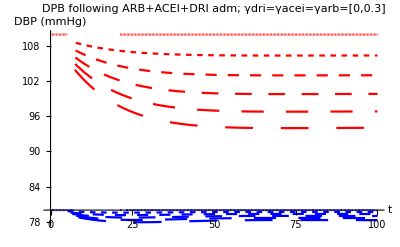

```mathematica
For[j=0,j<6,j++,For[i=0,i<2,i++,p[i][j]=Plot[Evaluate[Tension[i][t]/.sol[i][j]],{t,0,100},PlotStyle->{Color[i],Dashing[j/100]}]]];Show[p[0][0],p[0][1],p[0][2],p[0][3],p[0][4],p[0][5],
p[1][0],p[1][1],p[1][2],p[1][3],p[1][4],p[1][5],PlotRange->All,PlotLabel->"DPB following ARB+ACEI+DRI adm; γdri=γacei=γarb=[0,0.3]",AxesLabel->{"t","DBP (mmHg)"}]
```

Analysis of the impact of ACE-I and ARB drug combination on the DBP of hypertensive patients

```mathematica
For[k=0,k<41,k++,γacei=k*0.0125;
For[m=0,m<41,m++,γarb=m*0.0125;γdri=0;
EQS;
For[i=0,i<2,i++,sola[i][k][m]=Solve[{0==eqAGT[i],0==eqRE[i],0==eqAI[i],0==eqAII[i],
0==eqA17[i],0==eqAIV[i],0==eqAT1Rb[i],0==eqAT2Rb[i],0==eqMASb[i]},{AGT[i][t],RE[i][t],AI[i][t],AII[i][t],A17[i][t],AIV[i][t],AT1Rb[i][t],AT2Rb[i][t],MASb[i][t]}]]]];
```

```mathematica
ListPlot3D[Table[Table[{0.0125*k,0.0125m,(73.6+0.429 AT1Rb [i][t]/.sola[i][k][m][[1]])},{k,0,40},{m,0,40}],{i,1,1}],PlotStyle->{Darker[Green]},AxesLabel->{"γacei","γarb","      DBP(mmHg)   "}]
```

-Graphics3D-

## Section 4. Modeling SARS-COV-2 Infection

### Modeling SARS-COV-2 effect via γace2

```mathematica
Clear[γace2]
```

```mathematica
γace2[Ct_]:=1/(1+Exp[0.53Ct-0.53 31.47]);
```

Plot of the downregulation function γace2 as a function of the viral load Ct

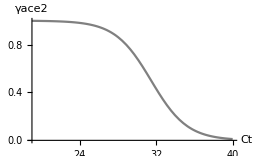

```mathematica
Plot[γace2[Ct],{Ct,19,40},PlotStyle->Gray,AxesLabel->{"Ct","γace2"}]
```

### Impact of SARS-COV-2 infection on RAS

```mathematica
For[i=0,i<2,i++,cace2f[i]=cace2[i]];
For[i=0,i<2,i++,cace2[i]=cace2f[i](baseline-γace2) ];
```

```mathematica
baseline=1;
```

```mathematica
For[j=1,j<201,j++,γace2=1/(1+Exp[0.53(j/10+20)-0.53 31.46847029814169]);γacei=0.0;γarb=0.0;
γdri=0.0;EQS;For[i=0,i<2,i++,sol[i][j]=NDSolve[{D[AGT[i][t],t]==eqAGT[i],D[RE[i][t],t]==eqRE[i],D[AI[i][t],t]==eqAI[i],D[AII[i][t],t]==eqAII[i],
D[A17[i][t],t]==eqA17[i],D[AIV[i][t],t]==eqAIV[i],D[AT1Rb[i][t],t]==eqAT1Rb[i],D[AT2Rb[i][t],t]==eqAT2Rb[i],D[MASb[i][t],t]==eqMASb[i],
AGT[i][0]==AGT0[i],RE[i][0]==RE0[i],AI[i][0]==AI0[i],AII[i][0]==AII0[i],A17[i][0]==A170[i],AIV[i][0]==AIV0[i],AT1Rb[i][0]==AT1Rb0[i],AT2Rb[i][0]==AT2Rb0[i],MASb[i][0]==MASb0[i]},{ AGT[i],RE[i],AI[i],AII[i],A17[i],AIV[i],AT1Rb[i],AT2Rb[i],MASb[i]},{t,0,100000}]]];
```

Plot of  A17 and AII concentration in COVID-19 patients as a function of the viral load Ct

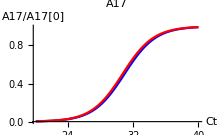

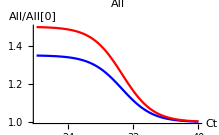

```mathematica
ListPlot[Table[{(j/10+20),(A17[i][100000]/A170[i]/.sol[i][j][[1]])},{i,0,1},{j,1,200}],Joined->True,PlotStyle->{Color[0],Color[1]},PlotLabel->"A17",PlotRange->All,AxesLabel->{"Ct","A17/A17[0]"}]
ListPlot[Table[{(j/10+20),(AII[i][100000]/AII0[i]/.sol[i][j][[1]])},{i,0,1},{j,1,200}],Joined->True,PlotStyle->{Color[0],Color[1]},PlotLabel->"AII",PlotRange->All,AxesLabel->{"Ct","AII/AII[0]"}]
```

Plot of PaO2/FiO2 in COVID-19 patients as a function of the viral load Ct

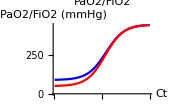

```mathematica
ListPlot[Table[{(j/10+20),267.0(- AII[i][t]/AII0[i]+ A17[i][t]/A170[i])+450.0/.t->100000/.sol[i][j][[1]]},{i,0,1},{j,1,200}],Joined->True,PlotStyle->{Color[0],Color[1]},PlotLabel->"PaO2/FiO2",PlotRange->All,AxesLabel->{"Ct","PaO2/FiO2 (mmHg)"}]
```

## Section 5. Modeling RAS-targeting drug effects on SARS-COV-2 Infection

```mathematica
tf=10000;
```

### ACE-I drug effect on SARS-COV-2 Infection

Plot of the value of PaO2/FiO2 (mmHg) in SARS-CoV-2 infected patients as a function of the viral load and γacei , which models the effects of ACE-I administration.

```mathematica
t=tf;
For[j=0,j<1,j++,γdri=j*0.0125;
For[k=0,k<41,k++,γacei=k*0.0125;
For[m=0,m<1,m++,γarb=m*0.0125;
For[n=0,n<201,n++,γace2=1/(1+Exp[0.53(n/10+20)-0.53 31.46847029814169]);
EQS;
For[i=0,i<2,i++,soltot[i][j][k][m][n]=Solve[{0==eqAGT[i],0==eqRE[i],0==eqAI[i],0==eqAII[i],
0==eqA17[i],0==eqAIV[i],0==eqAT1Rb[i],0==eqAT2Rb[i],0==eqMASb[i]},{ AGT[i][t],RE[i][t],AI[i][t],AII[i][t],A17[i][t],AIV[i][t],AT1Rb[i][t],AT2Rb[i][t],MASb[i][t]}]]]]]];
```

```mathematica
ListPlot3D[Table[Table[{k*0.0125,n/10+20,O2[i][tf]}/.soltot[i][0][k][0][n][[1]],{n,0,200},{k,0,40}],{i,0,1}],PlotStyle->Table[Color[i],{i,0,1}],AxesLabel->{"γacei","Ct"}]
```

-Graphics3D-

### ARB drug effect on SARS-COV-2 Infection

Plot of the value of PaO2/FiO2 (mmHg) in SARS-CoV-2 infected patients as a function of the viral load and γarb, which models the effects of ARB administration.

```mathematica
t=tf;
For[j=0,j<1,j++,γdri=j*0.0125;
For[k=0,k<1,k++,γacei=k*0.0125;
For[m=0,m<41,m++,γarb=m*0.0125;
For[n=0,n<201,n++,γace2=1/(1+Exp[0.53(n/10+20)-0.53 31.46847029814169]);
EQS;
For[i=0,i<2,i++,soltot[i][j][k][m][n]=Solve[{0==eqAGT[i],0==eqRE[i],0==eqAI[i],0==eqAII[i],
0==eqA17[i],0==eqAIV[i],0==eqAT1Rb[i],0==eqAT2Rb[i],0==eqMASb[i]},{ AGT[i][t],RE[i][t],AI[i][t],AII[i][t],A17[i][t],AIV[i][t],AT1Rb[i][t],AT2Rb[i][t],MASb[i][t]}]]]]]];
```

```mathematica
ListPlot3D[Table[Table[{m*0.0125,n/10+20,O2[i][tf]}/.soltot[i][0][0][m][n][[1]],{m,0,40},{n,0,200}],{i,0,1}],PlotStyle->Table[Color[i],{i,0,1}],AxesLabel->{"γarb","Ct"}]
```

-Graphics3D-

### DRI drug effect on SARS-COV-2 Infection

Plot of the value of PaO2/FiO2  (mmHg) in SARS-CoV-2 infected patients as a function of the viral load and γdri, which models the effects of DRI administration.

```mathematica
t=tf;
For[j=0,j<41,j++,γdri=j*0.0125;
For[k=0,k<1,k++,γacei=k*0.0125;
For[m=0,m<1,m++,γarb=m*0.0125;
For[n=0,n<201,n++,γace2=1/(1+Exp[0.53(n/10+20)-0.53 31.46847029814169]);
EQS;
For[i=0,i<2,i++,soltot[i][j][k][m][n]=Solve[{0==eqAGT[i],0==eqRE[i],0==eqAI[i],0==eqAII[i],
0==eqA17[i],0==eqAIV[i],0==eqAT1Rb[i],0==eqAT2Rb[i],0==eqMASb[i]},{ AGT[i][t],RE[i][t],AI[i][t],AII[i][t],A17[i][t],AIV[i][t],AT1Rb[i][t],AT2Rb[i][t],MASb[i][t]}]]]]]]
```

```mathematica
ListPlot3D[Table[Table[{j*0.0125,n/10+20,O2[i][tf]}/.soltot[i][j][0][0][n][[1]],{j,0,40},{n,0,200}],{i,0,1}],PlotStyle->Table[Color[i],{i,0,1}],AxesLabel->{"γdri","Ct"}]
```

-Graphics3D-

### rhACE2 drug effect on SARS-COV-2 Infection

Plot of the value of PaO2/FiO2 (mmHg) in SARS-CoV-2 infected patients as a function of the viral load and γrhACE2 , which models the effects of rhACE2 administration.

```mathematica
baseline=1+γrhACE2;
```

```mathematica
t=tf;
For[j=0,j<1,j++,γdri=j*0.0125;
For[k=0,k<1,k++,γacei=k*0.0125;
For[m=0,m<41,m++,γrhACE2=m*0.0125;
For[n=0,n<201,n++,γace2=1/(1+Exp[0.53(n/10+20)-0.53 31.46847029814169]);
EQS;
For[i=0,i<2,i++,soltot[i][j][k][m][n]=Solve[{0==eqAGT[i],0==eqRE[i],0==eqAI[i],0==eqAII[i],
0==eqA17[i],0==eqAIV[i],0==eqAT1Rb[i],0==eqAT2Rb[i],0==eqMASb[i]},{ AGT[i][t],RE[i][t],AI[i][t],AII[i][t],A17[i][t],AIV[i][t],AT1Rb[i][t],AT2Rb[i][t],MASb[i][t]}]]]]]];
```

```mathematica
ListPlot3D[Table[Table[{m*0.0125,n/10+20,O2[i][tf]}/.soltot[i][0][0][m][n][[1]],{m,0,40},{n,0,200}],{i,0,1}],PlotStyle->Table[Color[i],{i,0,1}],AxesLabel->{"γrhACE2","Ct"}]
```

-Graphics3D-

### Ang1-7 peptide effect on SARS-COV-2 Infection

Plot of the value of PaO2/FiO2 (mmHg) in SARS-CoV-2 infected patients as a function of the viral load and η , which models the effects of exogenous Ang17 administration.

```mathematica
baseline=1;
```

```mathematica
t=100000;
For[j=0,j<1,j++,
For[k=0,k<1,k++,
For[m=0,m<26,m++,
For[n=0,n<201,n++,γace2=1/(1+Exp[0.53(n/10+20)-0.53 31.46847029814169]);
EQS;
For[i=0,i<2,i++,solb[i][j][k][m][n]=Solve[{0==eqAGT[i],0==eqRE[i],0==eqAI[i],0==eqAII[i],
0==m+eqA17[i],0==eqAIV[i],0==eqAT1Rb[i],0==eqAT2Rb[i],0==eqMASb[i]},{ AGT[i][t],RE[i][t],AI[i][t],AII[i][t],A17[i][t],AIV[i][t],AT1Rb[i][t],AT2Rb[i][t],MASb[i][t]}]]]]]];
```

```mathematica
ListPlot3D[Table[Table[{m,n/10+20,O2[i][t]}/.solb[i][0][0][m][n][[1]],{m,0,25},{n,0,200}],{i,0,1}],PlotStyle->Table[Color[i],{i,0,1}],AxesLabel->{"η ang17","Ct"}]
```

-Graphics3D-